Articles for comparison:
R&I: https://arxiv.org/pdf/1202.2841.pdf
Dolgov et. al: https://arxiv.org/pdf/hep-ph/9703315.pdf
Mangano et. al: https://arxiv.org/pdf/hep-ph/0506164.pdf
Hannestad&Madsen: https://arxiv.org/pdf/astro-ph/9506015.pdf

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/Dropbox/victor_share/wolfram

```mathematica
FileToNumLevel2[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {2}]
];
```

```mathematica
FileToNumLevel1[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {1}]
];
```

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = FileToNumLevel2[linesEl];
```

```mathematica
T= Last[linesEl][[2]];
distEl1=Last[linesEl][[3;;]];
yEl=FileToNumLevel1[StringSplit[rawlinesEl[[1]]][[4;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

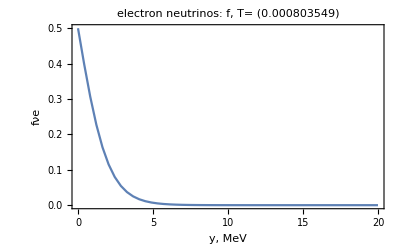

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electron neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνe"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ=FileToNumLevel2[linesμ];
```

```mathematica
Tμ= Last[linesμ][[2]];
distμ=Last[linesμ][[3;;]];
yμ=FileToNumLevel1[StringSplit[rawlinesμ[[1]]][[4;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

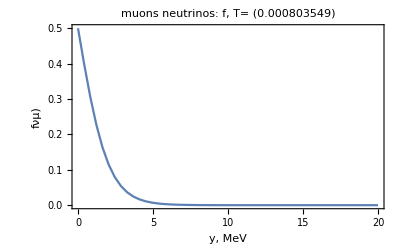

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνμ)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results (Fig. 10)

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
plotfEl=Interpolation[multiplier/@plotDataEl];
plotfμ=Interpolation[multiplier/@plotDataμ];
```

```mathematica
finalspectraSMTest=Import["../../figures/Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
```

Import::nffil: File not found during Import.

```mathematica
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
```

```mathematica
finalnueSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,8}]]];
```

```mathematica
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
```

InterpolatingFunction::dmval: Input value {0.000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

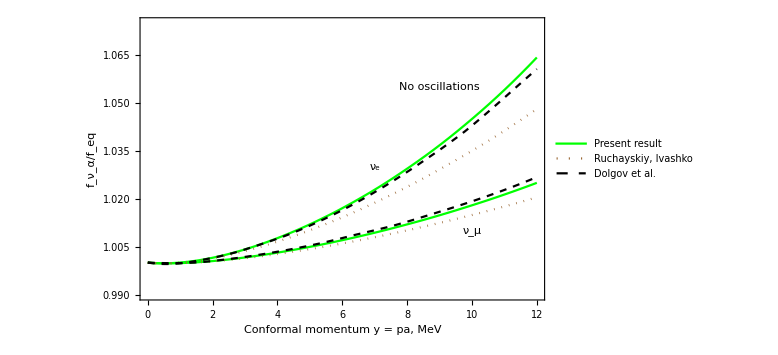

```mathematica
plt=Show[Plot[{
plotfEl[y],
plotfμ[y],
finalnueSMTestFunc[y],
finalnumuSMTestFunc[y],
finalspectranueSMDigitFunc[y],
finalspectranumuSMDigitFunc[y]
},{y,0,12},PlotRange->{{0,12},{0.99,1.075}},Frame->True,FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown,Dotted},{Brown,Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Dolgov et al.",None},ImageSize->Large]]
Export["final-spectra-SM.png",%];
```

### Mangano, Dolgov, Ruchaiskyi

```mathematica
ManganoNuEl=finalspectranueSMDigitFunc;
```

```mathematica
DolgovNuElBoltzmann=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovBoltzmann.csv"];
```

```mathematica
DolgovNuElFermi=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovFermi-Dirac.csv"];
```

```mathematica
DolgovNuElBoltzmannFunc=Interpolation[DolgovNuElBoltzmann];
DolgovNuElFermiFunc=Interpolation[DolgovNuElFermi];
```

InterpolatingFunction::dmval: Input value {0.000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

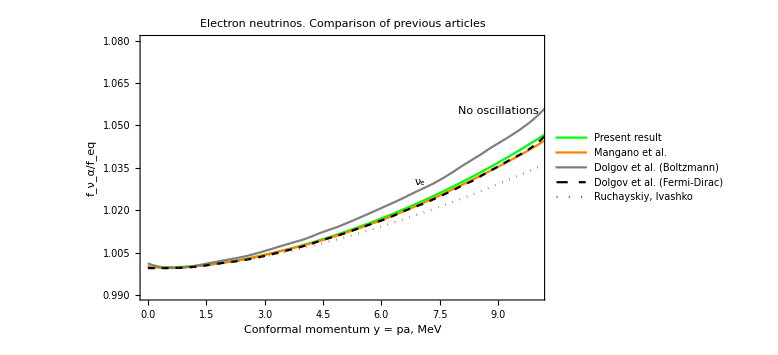

```mathematica
Show[Plot[{plotfEl[y],
ManganoNuEl[y],
DolgovNuElBoltzmannFunc[y]+1, DolgovNuElFermiFunc[y]+1, finalnueSMTestFunc[y]
},{y,0,12},PlotRange->{{0,10},{0.99,1.08}},Frame->True,PlotLabel-> "Electron neutrinos. Comparison of previous articles",FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green, Thick},{Orange, Thick},{Gray, Thick},{Black, Dashed}, {Brown,Dotted}},Epilog->{Text["ν_e",{7,1.03}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result","Mangano et al.","Dolgov et al. (Boltzmann)","Dolgov et al. (Fermi-Dirac)","Ruchayskiy, Ivashko"},ImageSize->Large]]
```

```mathematica
Export["Full-Comparison.png",%]
```

Full-Comparison.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Full-Comparison.png"]]]
```

## Final spectrum. Comparison with previous results (Fig. 11 of R&I article)

### Electron neutrinos

```mathematica
aEllist=First[Transpose[linesEl]];
```

```mathematica
setofdistributionsEl=Transpose[Transpose[linesEl][[3 ;;]]];
```

```mathematica
setofdistributionsEl1=Transpose[{yEl,#}]&/@setofdistributionsEl;
```

```mathematica
interpolatedDistEl=Interpolation/@setofdistributionsEl1;
```

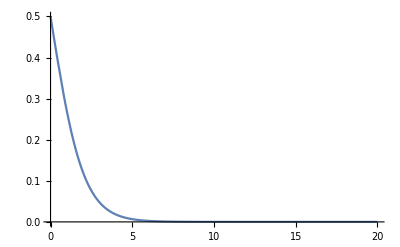

```mathematica
Plot[interpolatedDistEl[[20]][x],{x,0,20},PlotRange->All]
```

```mathematica
f3El=Interpolation[Transpose[{aEllist,#[3]&/@interpolatedDistEl}]];
f5El=Interpolation[Transpose[{aEllist,#[5]&/@interpolatedDistEl}]];
f7El=Interpolation[Transpose[{aEllist,#[7]&/@interpolatedDistEl}]];
```

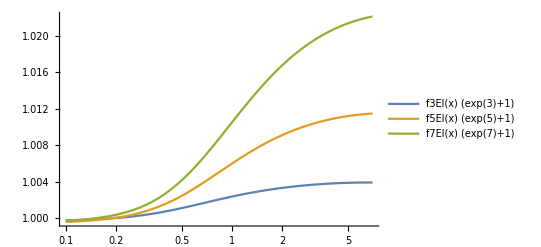

```mathematica
LogLinearPlot[{f3El[x]*(Exp[3]+1),f5El[x]*(Exp[5]+1),f7El[x]*(Exp[7]+1)},{x,0.1,7},PlotLegends->"Expressions"]
```

```mathematica
f3El[0.1]*(Exp[3]+1)-1
f5El[0.1]*(Exp[5]+1)-1
f7El[0.1]*(Exp[7]+1)-1
```

-0.000227875

-0.00040287

-0.000280664

```mathematica
(*sm-deltafnue_comp.eps*)
deltafnueTest=Import["../../figures/Figures-sources/sm-deltafnue_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnue3TestFunc=Interpolation[deltafnueTest[[All,{1,13}]]];
deltafnue5TestFunc=Interpolation[deltafnueTest[[All,{1,14}]]];
deltafnue7TestFunc=Interpolation[deltafnueTest[[All,{1,15}]]];
```

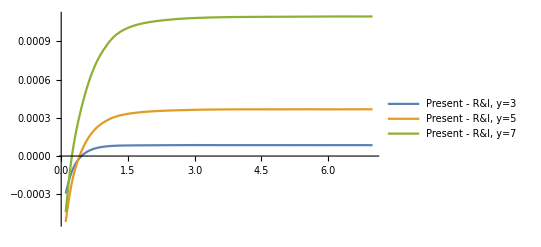

```mathematica
Show[Plot[{(f3El[x]-deltafnue3TestFunc[x])*(Exp[3]+1),(f5El[x]-deltafnue5TestFunc[x])*(Exp[5]+1),(f7El[x]-deltafnue7TestFunc[x])*(Exp[7]+1)},{x,0.1,7},PlotLegends->{"Present - R&I, y=3","Present - R&I, y=5","Present - R&I, y=7"}]]
```

```mathematica
deltafnue3Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue7-semi.dat","HeaderLines"->1];

deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
f7El[0.1]*(Exp[7]+1)-1
```

-0.000280664

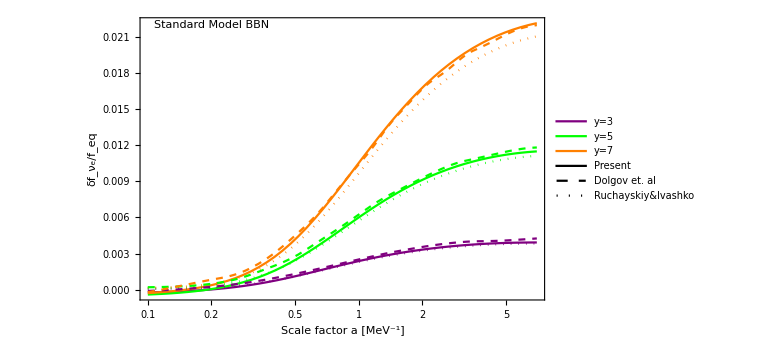

```mathematica
LogLinearPlot[{f3El[x]*(Exp[3]+1)-1,f5El[x]*(Exp[5]+1)-1,f7El[x]*(Exp[7]+1)-1,deltafnue3TestFunc[x]*(Exp[3]+1)-1,deltafnue5TestFunc[x]*(Exp[5]+1)-1,deltafnue7TestFunc[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,7},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_e/f_eq"},PlotStyle->{{Purple},{Green},{Orange},{Purple,Dotted},{Green,Dotted},{Orange,Dotted},{Purple,Dashed},{Green,Dashed},{Orange,Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.2],0.022}]},ImageSize->Large,PlotLegends->LineLegend[{Purple,Green,Orange,Thick,Dashed,Dotted},{"y=3","y=5","y=7","Present","Dolgov et. al","Ruchayskiy&Ivashko"}](*PlotLegends->{"Present, y=3","Present, y=5","Present, y=7","R&I, y=3","R&I, y=5","R&I, y=7","Dolgov, y=3","Dolgov, y=5","Dolgov, y=7"}*)]
```

```mathematica
Export["final-spectra-SM-357.png",%];
```

### Comparison with Fig 1 of Mangano’s paper

```mathematica
f10El=Interpolation[Transpose[{0.5*aEllist,#[10]&/@interpolatedDistEl}]];
```

```mathematica
f10El[0.1]*(Exp[10]+1)-1
```

0.000290106

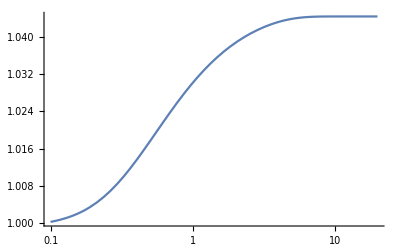

```mathematica
LogLinearPlot[f10El[x]*(Exp[10]+1),{x,0.1,20},Ticks -> Automatic]
```

```mathematica
deltafnue10Mangano=Import["mangano_dfn-y10.dat","HeaderLines"->1];
deltafnue10ManganoFunc=Interpolation[deltafnue10Mangano[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

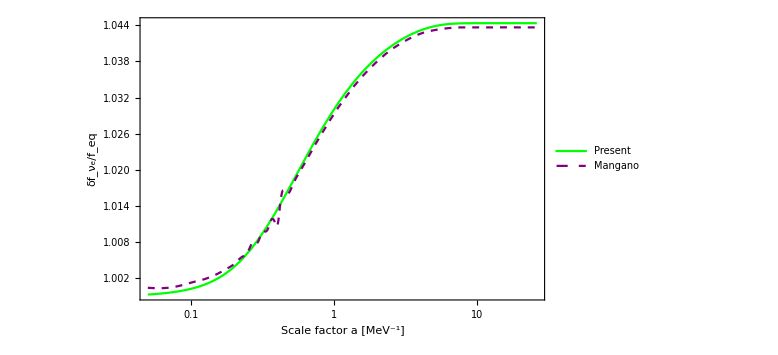

```mathematica
Show[LogLinearPlot[{f10El[x]*(Exp[10]+1),deltafnue10ManganoFunc[x]},{x,0.05,26},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_e/f_eq"},PlotStyle->{{Green},{Purple, Dashed}},Epilog->{Text["Standard Model BBN. y=10",{Log[0.2],0.022}]},ImageSize->Large,PlotLegends->{"Present","Mangano"}]]
```

## Convergence of the collision integral (draft)

```mathematica
rawlinesCollEl = Import["./output/Electron_neutrino.collision_integrals.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesCollEl = Rest[StringSplit/@rawlinesCollEl[[3;; ;; 10]]];
```

```mathematica
linesCollEl[[1]]
```

{0.000000000000000000e+00,-5.342315816392328998e-06,-2.343201330745614541e-06,1.993403486721945228e-06,5.254441468593995523e-06,6.890806591997034047e-06,7.181622319052394232e-06,6.630520319461652434e-06,5.678331378433654208e-06,4.624704073030727614e-06,3.638401215866338134e-06,2.789686577298056136e-06,2.099223808116335022e-06,1.556611954889319804e-06,1.141081925060127844e-06,8.289241693049120840e-07,5.975387448731162010e-07,4.280319201854787536e-07,3.050018994310566001e-07,2.163431593593667657e-07,1.528266720118853783e-07,1.075814069079195079e-07,7.549934611522646222e-08,5.283890627122422856e-08,3.688715071240022958e-08,2.569166532295774630e-08,1.785709650026917616e-08,1.238857786321767573e-08,8.580055028007543827e-09,5.932895673224983235e-09,4.096462092066308069e-09,2.824591841346126009e-09,1.945096162045065191e-09,1.337866860752576909e-09,9.191632172186534055e-10,6.308639704112172647e-10,4.325578819284504883e-10,2.963184872576156079e-10,2.028122430468379950e-10,1.386951982773674923e-10,9.477597731212647654e-11,6.471269981873526908e-11,4.415455699094579523e-11,3.010647040540680597e-11,2.051272032176879468e-11,1.396795895008913274e-11,9.504482440703227136e-12,6.462826162626408833e-12,4.391632375468998580e-12,2.981898146529070369e-12}

```mathematica
ICollEl = Map[Read[StringToStream[#],Number]&, linesCollEl, {2}];
```

```mathematica
yCollEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesCollEl[[1]]][[2;;]]];
```

```mathematica
Tlist=Select[Transpose[linesEl][[2]],#≤7&];
```

```mathematica
Length[Tlist]-Length[Max/@(Abs/@ICollEl)]
```

-45

```mathematica
Max/@(Abs/@ICollEl)
```

{7.18162231905239423×10^-6,0.0000102825804226824857,0.0000114165378839459208,0.0000121269477659780023,0.0000128690594536351455,0.0000134486109715226121,0.0000139116252384496875,0.0000142936588432007738,0.0000146213616503132471,0.0000149134576332698998,0.0000151826239402907959,0.0000154373074323643778,0.000015683113225861689,0.0000159237698937886307,0.0000161617704463878908,0.0000163987939316712073,0.0000166359796693882345,0.0000168741070538658278,0.0000171137138593735472,0.0000173551742932431807,0.0000175987514339226436,0.000017844631443608705,0.0000180929479753899614,0.0000183437976986056128,0.0000185972510990950468,0.0000188533604017493417,0.0000191121646508918275,0.0000193736930853560807,0.0000196379678740754571,0.0000199050056792771102,0.0000201748190420403262,0.0000204474176257463114,0.0000207228075765897302,0.0000210009941525868271,0.0000212819791300944416,0.0000215657633972909935,0.0000218523463146880204,0.0000221417256440759047,0.0000224338977616866941,0.0000227288578003026487,0.0000230265992229305994,0.0000233271145688718207,0.0000236303948497607053,0.000023936429869308995,0.0000242452079746158233,0.0000245567162338033995,0.0000248709399741642301,0.000025187864451936548,0.0000255074715838077282,0.000025829743037775188,0.000026154658776533779,0.0000264821974127471549,0.0000268123358537764034,0.000027145049550370004,0.0000274803122479738704,0.0000278180975854525059,0.0000281583749028868624,0.0000285011134693036183,0.0000288462810971168437,0.0000291938436802752221,0.0000295437651942620505,0.0000298960082645294278,0.0000302505337401726138,0.0000306073005518214814,0.0000309662659958576114,0.0000313273853436157879,0.000031690612622981007,0.0000320559015776211709,0.0000324231999471180643,0.0000327924566434489861,0.0000331636181272187969,0.000033536629509001159,0.0000339114332703616128,0.0000342879703651988166,0.0000346661800421088628,0.0000350459995246410472,0.0000354273661073989388,0.0000358102112585356736,0.0000361944669435843025,0.0000365895141740679719,0.0000370232190149977214,0.0000374598012342630682,0.0000378992172755943102,0.0000383414215932020852,0.0000387863664386145501,0.0000392340021093673386,0.0000396842770555849711,0.0000401371442393383404,0.0000405925420565722561,0.0000410504136993949942,0.0000415107002105230549,0.0000419733408030253941,0.0000424382720431992766,0.0000429054284012408971,0.000043374742499935337,0.0000438461448659666075,0.0000443195639832083543,0.0000447949263637781314,0.0000452721562815838752,0.0000457511760032502934,0.0000462319055749560448,0.0000467142633198136537,0.0000471981651273267744,0.0000476835246843165805,0.0000481702535637396068,0.000048658264208967239,0.0000491474713371076177,0.0000496377723990804043,0.0000501290720578140281,0.0000506212728268451428,0.0000511142743953030276,0.0000516079756707199522,0.0000521022740151977359,0.0000525970638776129817,0.0000530922376107412219,0.0000535876890239705972,0.0000540833088713554844,0.0000545789821515541007,0.0000550745950711473142,0.0000555700323623398163,0.0000560651768921616167,0.0000565599099999758437,0.0000570541158317894315,0.0000575476696518251174,0.0000580404431005376864,0.0000585323314794550242,0.0000590232009756164189,0.0000595129182379139365,0.0000600013615326133731,0.0000604884098009961235,0.0000609739246826279668,0.0000614577767699131528,0.0000619398355361511221,0.0000624199700283156744,0.0000628980485295471681,0.0000633739388433696149,0.0000638475080805278594,0.000064318621859627001,0.0000647871510039976783,0.0000652529587519268262,0.0000657159109351823645,0.00006617587287038873,0.0000666327094478447179,0.0000670862832130580955,0.0000675364440638759334,0.000067983139135918691,0.0000684261799044350028,0.0000688654314373593479,0.0000693007632079911673,0.0000697320455067540479,0.0000701591484464358928,0.0000705819434365650977,0.0000710003023662864052,0.000071414102862377149,0.0000718232170093813238,0.0000722275207110101292,0.0000726268907413896159,0.0000730212057753476529,0.0000734103462463053802,0.000073794193049536716,0.0000741726237407647204,0.0000745455371564673897,0.0000750199659194095148,0.0000754980722916798186,0.0000759718851028878817,0.000076441265672855252,0.0000769060765293261284,0.0000773661771447109459,0.0000778214349672623484,0.0000782717161307289189,0.0000787168875682198177,0.0000791568168878598044,0.0000795913726037156266,0.000080020423549598263,0.0000804438854018485472,0.0000808616009884133291,0.0000812734457866781668,0.0000816792773861152455,0.0000820789579947245329,0.0000824725016990157656,0.0000828597211111059551,0.0000832404968065247886,0.0000836147066074488521,0.0000839823006515416637,0.0000843431446639897331,0.0000846971367884918891,0.0000850441792010769859,0.0000853841779679953561,0.0000857170411272534238,0.0000860426759352606041,0.0000863609957946209761,0.0000866719593517473186,0.0000869754487631269058,0.0000872713502886313108,0.000087559713577434195,0.0000878403874793320938,0.0000881133209773565795,0.0000883785470229270231,0.0000886359127783009626,0.0000888853636915598599,0.0000891268495273322969,0.0000893603226259642725,0.0000895857386140619383,0.0000898030563867280307,0.0000900122370239841985,0.0000902132409486000597,0.0000904060241602167025,0.0000905905866943612637,0.0000907669024563517723,0.0000909350858080415492,0.0000910949893118129239,0.0000912465955771324389,0.0000913898885279706974,0.0000915247989574652365,0.0000916515223714498006,0.0000917700054081649341,0.0000918801911176103658,0.0000919820871203569368,0.0000920757028310958958,0.0000921610435256070559,0.0000922380820433943427,0.0000923069570646362081,0.0000923676562969433235,0.0000924201483165631998,0.0000924643516420076139,0.0000925007626761953361,0.0000925291198328181963,0.0000925494417458594398,0.0000925617622193897205,0.0000925661098882812894,0.0000925624881453757098,0.0000925508922122730837,0.000092531938484796683,0.0000925052575695417545,0.0000924708970195808888,0.0000924289083847895654,0.00009237936946959735,0.0000923223490723046325,0.0000922578907491811151,0.0000921860531022389296,0.0000921068848569461807,0.0000920203624588111779,0.0000919267541377166708,0.0000918263694593690616,0.0000917189408866647682,0.0000916043422272139196,0.0000914833937848413825,0.0000913557065906900334,0.0000912212390602462619,0.0000910803792031344983,0.000090933079430755015,0.0000907793791249389415,0.0000906193633909424534,0.0000904531184531265353,0.0000902807286529139219,0.0000901360592120425963,0.0000900256203806293343,0.0000899086449379637998,0.0000897850099068620011,0.0000896547648121526208,0.0000895178871473945037,0.0000893746447161447577,0.0000892254858442242949,0.0000890700885758377581,0.0000889085351207796748,0.0000887409215799550566,0.0000885673081629789749,0.0000883877834301216581,0.0000882024009118964614,0.0000880111690282348036,0.0000878141160232104312,0.0000876119907911032669,0.0000874045818299862276,0.0000871917810041367147,0.0000869736055086889337,0.0000867497346490608834,0.000086521596722732852,0.0000862885483865483138,0.0000860505314115300735,0.0000858073208487297734,0.0000855600731330952158,0.0000853083079999095162,0.0000850519673623040262,0.0000847908016865517311,0.0000845252120829087517,0.0000842552146718134054,0.0000839807139385584378,0.0000837029183120563403,0.0000834211198519341224,0.0000831353129449041717,0.0000828454444246062849,0.0000825510073010349288,0.0000822538663847183216,0.0000819544557817408759,0.0000816516381174636763,0.0000813454711767747085,0.0000810360347180960616,0.0000807234086686037244,0.0000804073631588408944,0.000080085462368373328,0.0000797603862601192759,0.0000794321227370886618,0.000079100802246045987,0.0000787673026270141463,0.000078430966281572978,0.0000780915472287091461,0.0000777487683212285674,0.0000774041750251086569,0.0000770599848021191747,0.0000767140329749338434,0.0000763659302904784454,0.0000760157496504376695,0.0000756635304099972927,0.0000753094364114303971,0.0000749534347743718854,0.0000745955374359397183,0.0000742357051386477451,0.0000738736566230357994,0.0000735094040482664468,0.0000731453538982407281,0.0000727804136868570595,0.0000724137254248802265,0.0000720413150734344754,0.0000716675659795384945,0.0000712938119828976369,0.0000709190050685037932,0.0000705425764380152032,0.0000701649461110065431,0.0000697850779562969592,0.00006940550324685546,0.0000690247875123617405,0.0000686398416949174361,0.0000682535366181014069,0.0000678650098073774188,0.0000674796722499593216,0.0000670937431479501356,0.0000667070349269494045,0.0000663193407657303169,0.0000659299359995202394,0.0000655389717429954999,0.0000651509393545524063,0.0000647614715898470195,0.0000643756757146007885,0.0000639890646603191726,0.0000636015977306669811,0.0000632135405886913304,0.0000628253582046767178,0.0000624368518664653038,0.0000620476282620074926,0.0000616567978894977387,0.0000612708505265402437,0.0000608847751948360383,0.0000604983561558469773,0.0000601110838438501105,0.0000597217488262913321,0.0000593251828195917597,0.00005893312299498632,0.0000585456110613336023,0.0000581578659364367923,0.0000577698206605248288,0.0000573784522917009099,0.000056993574304442518,0.0000566097899135087346,0.0000562257843839120142,0.000055841117063692991,0.0000554532231689108812,0.0000550725240433536101,0.0000546922529842674976,0.0000543116961004841414,0.0000539300611723803058,0.0000535481003449689297,0.0000531622309107859792,0.0000527847289433225342,0.0000524087324649258335,0.0000520312176366388712,0.0000516456792798436482,0.000051267862026804778,0.0000508877932947626732,0.0000505167794351280008,0.0000501460459023661542,0.0000497747251504421229,0.0000493966167436354908,0.0000490252960716475172,0.0000486555351209005949,0.0000482838242543692786,0.0000479095955174813071,0.0000475334344951505727,0.000047157696485555789,0.0000467809587512135749,0.0000464115917875318473,0.0000460377338651341006,0.0000456479070809479026,0.0000452846125487127438,0.0000449317809625426889,0.0000445790108738464141,0.0000442258966693032107,0.0000438719912843055226,0.0000435146816712972395,0.0000431641856213360597,0.0000428132464591612916,0.0000424602463944268038,0.0000421083860135951227,0.0000417548676345802505,0.0000413950458000300614,0.0000410337829315210456,0.0000406795541785243131,0.0000403165532780747071,0.0000399526377758974149,0.0000396190203932889062,0.0000392906047519403501,0.0000389617124874064302,0.0000386315412903570632,0.0000382967423107061222,0.0000379686091367403833,0.000037640940409033874,0.0000373133179021323258,0.0000369830750024391364,0.0000366416475383601892,0.0000362863500047438947,0.000035950624903691164,0.0000356106577559245352,0.0000352673804648873102,0.0000349144016453806216,0.0000345620011632519208,0.0000342292999544469012,0.0000339111414238146836,0.0000335807084539396783,0.000033242915415954144,0.0000328974752594746178,0.0000325666789890988184,0.0000322430222698955049,0.0000319167652218510511,0.000031586278472772733,0.0000312466321794602209,0.0000308920465208473161,0.0000305527476207601012,0.0000302167069676784195,0.0000298440578028191794,0.0000294851836368792419,0.0000291431152277255023,0.0000288048331320567286,0.0000284921340565347236,0.0000281774314547789118,0.0000278550575938396605,0.0000275038643149372319,0.0000271894036263375938,0.000026887921729112918,0.0000265814695499244635,0.0000262623751456914079,0.0000259213756148568564,0.0000255533288306963868,0.0000252264679634350841,0.0000248897150090243713,0.0000245316742297774226,0.0000242402452599321805,0.0000239226760001542971,0.000023640478934439102,0.0000233610700295372453,0.0000230695001679492862,0.0000227657471274511636,0.000022438723465967314,0.0000221317466220227743,0.0000218273004648494862,0.0000215002933146024589,0.0000212006247846119322,0.0000209477854884454473,0.0000206941476221800258,0.0000204380405044446434,0.0000201747587080802759,0.0000198954472718781972,0.0000195762898957951848,0.0000192666236120686563,0.0000189894493374254125,0.0000187176056787308198,0.0000184320861595921315,0.0000181250990838321968,0.0000178552488616645633,0.000017542300314588033,0.0000172350610938565296,0.0000169563447727227867,0.0000167208875545554747,0.000016480701257037822,0.0000162287409732897459,0.0000159582112324585523,0.0000156790464611589187,0.000015354940510192705,0.000015038722915861058,0.0000147724460219933462,0.000014509501964354854,0.0000142429861949011638,0.0000139666482201761255,0.0000137037810787887793,0.000013415538884231637,0.0000131701792938088147,0.0000129078726018860834,0.0000126870941663526082,0.0000124581658145217489,0.0000121959223076117951,0.000011942058630864949,0.0000116938328353910492,0.0000114293742248250396,0.0000111899443400176324,0.0000109406269555023528,0.0000107580436159437909,0.0000105731278354781466,0.0000103704003828752889,0.0000101354400916520149,9.88902142395886585×10^-6,9.68887363228532195×10^-6,9.46775669863342273×10^-6,9.22903472311276119×10^-6,9.0212565906355735×10^-6,8.83590177469528726×10^-6,8.66087702888762578×10^-6,8.54607982603283745×10^-6,8.42860213623453092×10^-6,8.31448495830500178×10^-6,8.20474703289164609×10^-6,8.09408415847201468×10^-6,7.97872349522776858×10^-6,7.86361532334467484×10^-6,7.73935052933438783×10^-6,7.60542590683144226×10^-6,7.47398384959296891×10^-6,7.34325865892060392×10^-6,7.21305564610474903×10^-6,7.08727881715276453×10^-6,6.96163791502613094×10^-6,6.83084085295604382×10^-6,6.70108672551350537×10^-6,6.56618315275636633×10^-6,6.43156496948904533×10^-6,6.29808099006368138×10^-6,6.16672874542700811×10^-6,6.03831061596338259×10^-6,5.91023027851633742×10^-6,5.78207714596601363×10^-6,5.65172637578825743×10^-6,5.52168710754585845×10^-6,5.39471532334800941×10^-6,5.26929859745450813×10^-6,5.14616253610711283×10^-6,5.02410042457768213×10^-6,4.90243674988732892×10^-6,4.78131024550521033×10^-6,4.66241189656102506×10^-6,4.54504792912757694×10^-6,4.4299041945805584×10^-6,4.31680263091038796×10^-6,4.20521860888811716×10^-6,4.0947783119804626×10^-6,3.9862799283696404×10^-6,3.87996138329071982×10^-6,3.77574213672460246×10^-6,3.673457840136507×10^-6,3.5725600966429738×10^-6,3.47357300256589952×10^-6,3.39009435634807232×10^-6,3.30916648749735032×10^-6,3.22964289978244779×10^-6,3.1511540399264959×10^-6,3.07409234068245496×10^-6,2.99656868207875959×10^-6,2.91841043775775688×10^-6,2.84179446197185825×10^-6,2.76721703329485536×10^-6,2.69353769510871643×10^-6,2.62147658247613435×10^-6,2.54936782795311956×10^-6,2.47805122199906691×10^-6,2.40847121801834874×10^-6,2.34031155343927821×10^-6,2.27342557224119446×10^-6,2.20776218640139632×10^-6,2.14286760780169061×10^-6,2.07936754037518767×10^-6,2.01737790916922677×10^-6,1.95671752578618907×10^-6,1.8973324245052936×10^-6,1.83891764038435213×10^-6,1.78196359001958626×10^-6,1.72642668161415713×10^-6,1.67213858759396317×10^-6,1.61893325412165723×10^-6,1.56708676257721891×10^-6,1.51655530800098859×10^-6,1.46724413951915267×10^-6,1.4191184405376589×10^-6,1.37225732999013417×10^-6,1.32660144203100572×10^-6,1.28209606486962002×10^-6,1.23875349089530573×10^-6,1.19658427166768888×10^-6,1.15552801105422986×10^-6,1.11558499327202298×10^-6,1.07672903482125548×10^-6,1.03894212344357584×10^-6,1.00221786425436221×10^-6,9.66534479118763557×10^-7,9.31883867849592207×10^-7,8.9823437576797005×10^-7,8.65566427421526896×10^-7,8.33859203908104973×10^-7,8.03087338852037647×10^-7,7.732559126338856×10^-7,7.44325703294634877×10^-7,7.16269532574642653×10^-7,6.89068109238633042×10^-7,6.62704060516716709×10^-7,6.37170636252903933×10^-7,6.12435080427076173×10^-7,5.88481263719131675×10^-7,5.65313698075442517×10^-7,5.42907265810299577×10^-7,5.21230809624739777×10^-7,5.00276478021532967×10^-7,4.80018869097875722×10^-7,4.60440006122553314×10^-7,4.41525571659440175×10^-7,4.23246788727738021×10^-7,4.05587918805849768×10^-7,3.88533329953588691×10^-7,3.72074353549578518×10^-7,3.56196245832052227×10^-7,3.40875665472140099×10^-7,3.26099396374956996×10^-7,3.1187273208388433×10^-7,2.98176168200825487×10^-7,2.84983379117420554×10^-7,2.72289781833023881×10^-7,2.60069370483506646×10^-7,2.48309888206676988×10^-7,2.37002453218337905×10^-7,2.26127561120392784×10^-7,2.15669047065603081×10^-7,2.05615400261649484×10^-7,1.95954292792066553×10^-7,1.86676274438468681×10^-7,1.77773848974993598×10^-7,1.69228719926195481×10^-7,1.6103467004313643×10^-7,1.53191024310217472×10^-7,1.45680552066096425×10^-7,1.38484281819728494×10^-7,1.31596635810637963×10^-7,1.25005321649496182×10^-7,1.18695702155946492×10^-7,1.12661950879555661×10^-7,1.06897140028650028×10^-7,1.01386774531420087×10^-7,9.61205515181973169×10^-8,9.10901576389733236×10^-8,8.62872440166029264×10^-8,8.17034617739409441×10^-8,7.73324870806391118×10^-8,7.31699145717357169×10^-8,6.92119428435944428×10^-8,6.54451426385094237×10^-8,6.18625151105334226×10^-8,5.84531179015357338×10^-8,5.52099876927059086×10^-8,5.21297849331858743×10^-8,4.92022067533071095×10^-8,4.64212845940892294×10^-8,4.37811920050990011×10^-8,4.1276813078638952×10^-8,3.89045951010302815×10^-8,3.66554431252552604×10^-8,3.45239214993853238×10^-8,3.25048787885862112×10^-8,3.05935188293915417×10^-8,2.8787212613679003×10^-8,2.70825140091801586×10^-8,2.54733478755042597×10^-8,2.39542785607227415×10^-8,2.25210428084210435×10^-8,2.11685957651752688×10^-8,1.98924610117501288×10^-8,1.86890503073300351×10^-8,1.75561609694341314×10^-8,1.64889613074592489×10^-8,1.54838986077265872×10^-8,1.45379885907459538×10^-8,1.36481048684800044×10^-8,1.28115118513960624×10^-8,1.20259358027396957×10^-8,1.12885345515678637×10^-8,1.05965369812111021×10^-8,9.94877069615540677×10^-9,9.34157640131161315×10^-9,8.77243166996777291×10^-9,8.23934698246375774×10^-9,7.73983543922440731×10^-9,7.27194304772638134×10^-9,6.8858341251143429×10^-9,6.52676135359797627×10^-9,6.19003515112126479×10^-9,5.87402126939196023×10^-9,5.57726309580175439×10^-9,5.2986237619734311×10^-9,5.03714403521371423×10^-9,4.7915449385982356×10^-9,4.56097382084408309×10^-9,4.34475566635228461×10^-9,4.14242862234459608×10^-9,3.95257160334949731×10^-9,3.7745095937680162×10^-9,3.60735441518045263×10^-9,3.47185391547100153×10^-9,3.35518279825919308×10^-9,3.24405391438631341×10^-9,3.13804093821090646×10^-9,3.03721492400654825×10^-9,2.94122060040535871×10^-9,2.84991585886018584×10^-9,2.76273226518242154×10^-9,2.67917243945703376×10^-9,2.59944954450475052×10^-9,2.52292409186338773×10^-9,2.44973819008009741×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ICollMaximums=Transpose[{Tlist,Max/@(Abs/@ICollEl)}]
```

Transpose::nmtx: The first two levels of {{6.98682,6.93246,6.87852,6.825,6.77189,6.7192,6.66692,6.61504,6.56357,6.5125,6.46183,6.41155,6.36166,6.31217,6.26305,6.21432,6.16597,«18»,5.31556,5.27421,5.23317,5.19246,5.15206,5.11198,5.07221,5.03275,4.99359,4.95474,4.9162,4.87795,4.84,4.80235,4.76499,«1155»},{«1»}} cannot be transposed.

Transpose[{{6.98682,6.93246,6.87852,6.825,6.77189,6.7192,6.66692,6.61504,6.56357,6.5125,6.46183,6.41155,6.36166,6.31217,6.26305,6.21432,6.16597,6.11799,6.07039,6.02316,5.9763,5.9298,5.88366,5.83788,5.79246,5.74739,5.70268,5.65831,5.61428,5.5706,5.52726,5.48426,5.44159,5.39925,5.35724,5.31556,5.27421,5.23317,5.19246,5.15206,5.11198,5.07221,5.03275,4.99359,4.95474,4.9162,4.87795,4.84,4.80235,4.76499,4.72792,4.69113,4.65464,4.61843,4.5825,4.54685,4.51148,4.47638,4.44156,4.40701,4.37273,4.33871,4.30496,4.27147,4.23825,4.20528,4.17256,4.14011,4.1079,4.07595,4.04424,4.01279,3.98157,3.9506,3.91987,3.88938,3.85913,3.82912,3.79933,3.76978,3.74046,3.71137,3.6825,3.65386,3.62544,3.59725,3.56927,3.54151,3.51397,3.48664,3.45953,3.43262,3.40593,3.37944,3.35316,3.32708,3.30121,3.27554,3.25007,3.2248,3.19972,3.17484,3.15015,3.12566,3.10136,3.07724,3.05332,3.02958,3.00602,2.98265,2.95946,2.93645,2.91362,2.89097,2.8685,2.8462,2.82407,2.80212,2.78034,2.75872,2.73728,2.716,2.69489,2.67395,2.65316,2.63254,2.61208,2.59178,2.57164,2.55165,2.53182,2.51215,2.49263,2.47326,2.45404,2.43497,2.41605,2.39728,2.37865,2.36017,2.34183,2.32364,2.30559,2.28768,2.26991,2.25227,2.23478,2.21742,2.2002,2.18311,2.16615,2.14933,2.13264,2.11608,2.09965,2.08334,2.06717,2.05112,2.03519,2.01939,2.00371,1.98816,1.97272,1.95741,1.94222,1.92714,1.91219,1.89735,1.88262,1.86801,1.85352,1.83913,1.82487,1.81071,1.79666,1.78272,1.76889,1.75517,1.74156,1.72805,1.71465,1.70135,1.68816,1.67507,1.66208,1.6492,1.63641,1.62372,1.61114,1.59865,1.58626,1.57397,1.56177,1.54967,1.53766,1.52575,1.51393,1.5022,1.49057,1.47902,1.46757,1.4562,1.44493,1.43374,1.42264,1.41163,1.4007,1.38986,1.37911,1.36844,1.35785,1.34734,1.33692,1.32658,1.31632,1.30614,1.29604,1.28602,1.27608,1.26621,1.25643,1.24672,1.23708,1.22752,1.21804,1.20863,1.1993,1.19003,1.18085,1.17173,1.16268,1.15371,1.14481,1.13597,1.12721,1.11851,1.10988,1.10132,1.09283,1.08441,1.07605,1.06775,1.05952,1.05136,1.04326,1.03523,1.02725,1.01934,1.0115,1.00371,0.995985,0.988321,0.980717,0.973174,0.96569,0.958265,0.950898,0.943589,0.936338,0.929145,0.922008,0.914927,0.907902,0.900932,0.894018,0.887158,0.880352,0.873599,0.866901,0.860255,0.853661,0.84712,0.84063,0.834192,0.827804,0.821467,0.81518,0.808943,0.802755,0.796616,0.790526,0.784484,0.77849,0.772543,0.766643,0.76079,0.754984,0.749223,0.743508,0.737839,0.732214,0.726634,0.721098,0.715606,0.710158,0.704753,0.699391,0.694071,0.688794,0.683559,0.678365,0.673213,0.668102,0.663031,0.658,0.65301,0.648059,0.643148,0.638276,0.633443,0.628648,0.623891,0.619173,0.614492,0.609848,0.605242,0.600672,0.596138,0.591641,0.58718,0.582754,0.578364,0.574009,0.569688,0.565403,0.561151,0.556934,0.55275,0.5486,0.544483,0.540399,0.536347,0.532329,0.528342,0.524387,0.520464,0.516573,0.512713,0.508884,0.505085,0.501317,0.497579,0.493872,0.490194,0.486546,0.482927,0.479337,0.475776,0.472244,0.46874,0.465264,0.461817,0.458397,0.455005,0.45164,0.448302,0.444991,0.441707,0.438449,0.435218,0.432013,0.428833,0.42568,0.422551,0.419448,0.41637,0.413317,0.410289,0.407285,0.404306,0.40135,0.398419,0.395511,0.392627,0.389766,0.386928,0.384113,0.381321,0.378552,0.375805,0.37308,0.370378,0.367697,0.365038,0.362401,0.359785,0.35719,0.354616,0.352063,0.349531,0.347019,0.344528,0.342057,0.339606,0.337175,0.334763,0.332371,0.329999,0.327645,0.325311,0.322996,0.320699,0.318421,0.316162,0.313921,0.311698,0.309493,0.307305,0.305136,0.302984,0.30085,0.298733,0.296633,0.29455,0.292483,0.290434,0.288401,0.286384,0.284384,0.2824,0.280432,0.27848,0.276543,0.274622,0.272717,0.270827,0.268952,0.267093,0.265248,0.263418,0.261603,0.259802,0.258016,0.256244,0.254486,0.252742,0.251013,0.249297,0.247595,0.245906,0.244231,0.242569,0.24092,0.239285,0.237663,0.236053,0.234456,0.232872,0.2313,0.229741,0.228194,0.22666,0.225137,0.223627,0.222128,0.220641,0.219166,0.217702,0.21625,0.214809,0.213379,0.21196,0.210553,0.209156,0.207771,0.206396,0.205031,0.203677,0.202334,0.201001,0.199678,0.198365,0.197063,0.19577,0.194487,0.193214,0.191951,0.190697,0.189453,0.188218,0.186992,0.185776,0.184568,0.18337,0.182181,0.181001,0.179829,0.178666,0.177512,0.176366,0.175229,0.1741,0.172979,0.171867,0.170762,0.169666,0.168577,0.167497,0.166424,0.165359,0.164302,0.163252,0.16221,0.161175,0.160147,0.159127,0.158114,0.157108,0.156109,0.155117,0.154132,0.153154,0.152183,0.151218,0.15026,0.149308,0.148363,0.147424,0.146492,0.145566,0.144646,0.143732,0.142825,0.141923,0.141028,0.140138,0.139254,0.138376,0.137504,0.136637,0.135776,0.13492,0.13407,0.133226,0.132386,0.131552,0.130723,0.1299,0.129081,0.128268,0.12746,0.126656,0.125858,0.125064,0.124275,0.123491,0.122712,0.121937,0.121167,0.120402,0.119641,0.118884,0.118132,0.117384,0.116641,0.115901,0.115166,0.114436,0.113709,0.112986,0.112268,0.111553,0.110843,0.110136,0.109433,0.108734,0.108039,0.107347,0.10666,0.105976,0.105295,0.104618,0.103945,0.103275,0.102609,0.101946,0.101287,0.100631,0.0999784,0.0993291,0.0986831,0.0980404,0.0974009,0.0967646,0.0961314,0.0955014,0.0948745,0.0942507,0.0936299,0.0930122,0.0923975,0.0917858,0.091177,0.0905712,0.0899683,0.0893683,0.0887712,0.0881769,0.0875854,0.0869968,0.0864109,0.0858279,0.0852476,0.08467,0.0840952,0.0835231,0.0829537,0.082387,0.081823,0.0812617,0.080703,0.0801469,0.0795935,0.0790428,0.0784946,0.0779491,0.0774062,0.0768659,0.0763282,0.0757931,0.0752605,0.0747306,0.0742032,0.0736785,0.0731563,0.0726367,0.0721197,0.0716053,0.0710934,0.0705842,0.0700775,0.0695734,0.0690719,0.068573,0.0680767,0.067583,0.0670919,0.0666034,0.0661175,0.0656342,0.0651536,0.0646756,0.0642002,0.0637275,0.0632574,0.0627899,0.0623251,0.061863,0.0614035,0.0609467,0.0604925,0.0600411,0.0595923,0.0591462,0.0587028,0.058262,0.057824,0.0573887,0.0569561,0.0565262,0.056099,0.0556745,0.0552527,0.0548336,0.0544173,0.0540036,0.0535927,0.0531844,0.0527789,0.0523761,0.051976,0.0515786,0.0511839,0.0507919,0.0504026,0.050016,0.049632,0.0492508,0.0488722,0.0484962,0.048123,0.0477524,0.0473844,0.0470191,0.0466563,0.0462963,0.0459388,0.0455839,0.0452316,0.0448819,0.0445347,0.0441901,0.0438481,0.0435086,0.0431716,0.0428371,0.0425051,0.0421756,0.0418486,0.041524,0.0412019,0.0408822,0.0405649,0.0402501,0.0399376,0.0396274,0.0393197,0.0390143,0.0387112,0.0384104,0.038112,0.0378158,0.0375219,0.0372302,0.0369408,0.0366536,0.0363687,0.0360859,0.0358053,0.0355268,0.0352506,0.0349764,0.0347044,0.0344344,0.0341666,0.0339008,0.0336371,0.0333754,0.0331158,0.0328581,0.0326025,0.0323488,0.0320972,0.0318474,0.0315996,0.0313538,0.0311098,0.0308677,0.0306275,0.0303892,0.0301528,0.0299181,0.0296853,0.0294543,0.0292251,0.0289977,0.0287721,0.0285482,0.028326,0.0281056,0.0278869,0.0276699,0.0274545,0.0272409,0.0270289,0.0268186,0.0266099,0.0264028,0.0261973,0.0259934,0.0257912,0.0255905,0.0253913,0.0251937,0.0249977,0.0248031,0.0246101,0.0244186,0.0242286,0.02404,0.0238529,0.0236673,0.0234831,0.0233004,0.0231191,0.0229392,0.0227606,0.0225835,0.0224078,0.0222334,0.0220604,0.0218887,0.0217184,0.0215493,0.0213816,0.0212152,0.0210502,0.0208863,0.0207238,0.0205625,0.0204025,0.0202437,0.0200862,0.0199299,0.0197748,0.0196209,0.0194682,0.0193167,0.0191664,0.0190172,0.0188692,0.0187224,0.0185767,0.0184321,0.0182887,0.0181464,0.0180051,0.017865,0.017726,0.0175881,0.0174512,0.0173154,0.0171806,0.0170469,0.0169143,0.0167826,0.016652,0.0165225,0.0163939,0.0162663,0.0161397,0.0160141,0.0158895,0.0157658,0.0156431,0.0155214,0.0154006,0.0152808,0.0151619,0.0150439,0.0149268,0.0148106,0.0146954,0.014581,0.0144675,0.014355,0.0142432,0.0141324,0.0140224,0.0139133,0.013805,0.0136976,0.013591,0.0134852,0.0133803,0.0132762,0.0131728,0.0130703,0.0129686,0.0128677,0.0127676,0.0126682,0.0125696,0.0124718,0.0123747,0.0122784,0.0121829,0.0120881,0.011994,0.0119007,0.0118081,0.0117162,0.011625,0.0115345,0.0114448,0.0113557,0.0112673,0.0111797,0.0110927,0.0110063,0.0109207,0.0108357,0.0107514,0.0106677,0.0105847,0.0105023,0.0104206,0.0103395,0.010259,0.0101792,0.0101,0.0100214,0.00994339,0.009866,0.00978923,0.00971305,0.00963746,0.00956246,0.00948804,0.00941421,0.00934095,0.00926825,0.00919613,0.00912456,0.00905356,0.0089831,0.00891319,0.00884383,0.00877501,0.00870672,0.00863896,0.00857173,0.00850503,0.00843884,0.00837317,0.00830801,0.00824336,0.00817921,0.00811555,0.0080524,0.00798973,0.00792756,0.00786587,0.00780465,0.00774392,0.00768365,0.00762386,0.00756453,0.00750566,0.00744725,0.0073893,0.00733179,0.00727474,0.00721812,0.00716195,0.00710622,0.00705092,0.00699605,0.0069416,0.00688758,0.00683398,0.0067808,0.00672803,0.00667567,0.00662372,0.00657218,0.00652103,0.00647028,0.00641993,0.00636997,0.0063204,0.00627121,0.00622241,0.00617399,0.00612594,0.00607827,0.00603097,0.00598403,0.00593747,0.00589126,0.00584541,0.00579993,0.00575479,0.00571001,0.00566557,0.00562148,0.00557773,0.00553433,0.00549126,0.00544853,0.00540612,0.00536405,0.00532231,0.00528089,0.0052398,0.00519902,0.00515856,0.00511842,0.00507858,0.00503906,0.00499985,0.00496094,0.00492233,0.00488403,0.00484602,0.00480831,0.00477089,0.00473376,0.00469692,0.00466037,0.0046241,0.00458812,0.00455241,0.00451699,0.00448184,0.00444696,0.00441235,0.00437801,0.00434394,0.00431014,0.0042766,0.00424332,0.00421029,0.00417753,0.00414502,0.00411276,0.00408076,0.004049,0.00401749,0.00398623,0.00395521,0.00392443,0.00389389,0.00386358,0.00383352,0.00380368,0.00377408,0.00374471,0.00371557,0.00368666,0.00365797,0.0036295,0.00360126,0.00357323,0.00354542,0.00351783,0.00349046,0.00346329,0.00343634,0.0034096,0.00338307,0.00335674,0.00333062,0.0033047,0.00327898,0.00325346,0.00322814,0.00320302,0.0031781,0.00315336,0.00312883,0.00310448,0.00308032,0.00305635,0.00303256,0.00300896,0.00298555,0.00296231,0.00293926,0.00291639,0.00289369,0.00287117,0.00284883,0.00282666,0.00280466,0.00278283,0.00276118,0.00273969,0.00271837,0.00269722,0.00267623,0.0026554,0.00263474,0.00261423,0.00259389,0.0025737,0.00255367,0.0025338,0.00251408,0.00249452,0.0024751,0.00245584,0.00243673,0.00241777,0.00239895,0.00238028,0.00236176,0.00234338,0.00232515,0.00230705,0.0022891,0.00227128,0.00225361,0.00223607,0.00221867,0.0022014,0.00218427,0.00216727,0.00215041,0.00213367,0.00211707,0.00210059,0.00208425,0.00206803,0.00205193,0.00203597,0.00202012,0.0020044,0.0019888,0.00197333,0.00195797,0.00194273,0.00192761,0.00191261,0.00189773,0.00188296,0.00186831,0.00185377,0.00183934,0.00182503,0.00181083,0.00179673,0.00178275,0.00176888,0.00175511,0.00174145,0.0017279,0.00171446,0.00170111,0.00168787,0.00167474,0.00166171,0.00164878,0.00163594,0.00162321,0.00161058,0.00159805,0.00158561,0.00157327,0.00156103,0.00154888,0.00153683,0.00152487,0.001513,0.00150123,0.00148954,0.00147795,0.00146645,0.00145504,0.00144372,0.00143248,0.00142133,0.00141027,0.0013993,0.00138841,0.0013776,0.00136688,0.00135625,0.00134569,0.00133522,0.00132483,0.00131452,0.00130429,0.00129414,0.00128407,0.00127407,0.00126416,0.00125432,0.00124456,0.00123488,0.00122527,0.00121573,0.00120627,0.00119688,0.00118757,0.00117833,0.00116916,0.00116006,0.00115103,0.00114207,0.00113319,0.00112437,0.00111562,0.00110694,0.00109832,0.00108977,0.00108129,0.00107288,0.00106453,0.00105625,0.00104803,0.00103987,0.00103178,0.00102375,0.00101578,0.00100788,0.00100003,0.00099225,0.000984528,0.000976867,0.000969265,0.000961722,0.000954238,0.000946812,0.000939444,0.000932133,0.000924879,0.000917681,0.00091054,0.000903454,0.000896423,0.000889447,0.000882526,0.000875658,0.000868843,0.000862082,0.000855373,0.000848717,0.000842112,0.000835558,0.000829056,0.000822604,0.000816203,0.000809851,0.000803549},{7.18162231905239423×10^-6,0.0000102825804226824857,0.0000114165378839459208,0.0000121269477659780023,0.0000128690594536351455,0.0000134486109715226121,0.0000139116252384496875,0.0000142936588432007738,0.0000146213616503132471,0.0000149134576332698998,0.0000151826239402907959,0.0000154373074323643778,0.000015683113225861689,0.0000159237698937886307,0.0000161617704463878908,0.0000163987939316712073,0.0000166359796693882345,0.0000168741070538658278,0.0000171137138593735472,0.0000173551742932431807,0.0000175987514339226436,0.000017844631443608705,0.0000180929479753899614,0.0000183437976986056128,0.0000185972510990950468,0.0000188533604017493417,0.0000191121646508918275,0.0000193736930853560807,0.0000196379678740754571,0.0000199050056792771102,0.0000201748190420403262,0.0000204474176257463114,0.0000207228075765897302,0.0000210009941525868271,0.0000212819791300944416,0.0000215657633972909935,0.0000218523463146880204,0.0000221417256440759047,0.0000224338977616866941,0.0000227288578003026487,0.0000230265992229305994,0.0000233271145688718207,0.0000236303948497607053,0.000023936429869308995,0.0000242452079746158233,0.0000245567162338033995,0.0000248709399741642301,0.000025187864451936548,0.0000255074715838077282,0.000025829743037775188,0.000026154658776533779,0.0000264821974127471549,0.0000268123358537764034,0.000027145049550370004,0.0000274803122479738704,0.0000278180975854525059,0.0000281583749028868624,0.0000285011134693036183,0.0000288462810971168437,0.0000291938436802752221,0.0000295437651942620505,0.0000298960082645294278,0.0000302505337401726138,0.0000306073005518214814,0.0000309662659958576114,0.0000313273853436157879,0.000031690612622981007,0.0000320559015776211709,0.0000324231999471180643,0.0000327924566434489861,0.0000331636181272187969,0.000033536629509001159,0.0000339114332703616128,0.0000342879703651988166,0.0000346661800421088628,0.0000350459995246410472,0.0000354273661073989388,0.0000358102112585356736,0.0000361944669435843025,0.0000365895141740679719,0.0000370232190149977214,0.0000374598012342630682,0.0000378992172755943102,0.0000383414215932020852,0.0000387863664386145501,0.0000392340021093673386,0.0000396842770555849711,0.0000401371442393383404,0.0000405925420565722561,0.0000410504136993949942,0.0000415107002105230549,0.0000419733408030253941,0.0000424382720431992766,0.0000429054284012408971,0.000043374742499935337,0.0000438461448659666075,0.0000443195639832083543,0.0000447949263637781314,0.0000452721562815838752,0.0000457511760032502934,0.0000462319055749560448,0.0000467142633198136537,0.0000471981651273267744,0.0000476835246843165805,0.0000481702535637396068,0.000048658264208967239,0.0000491474713371076177,0.0000496377723990804043,0.0000501290720578140281,0.0000506212728268451428,0.0000511142743953030276,0.0000516079756707199522,0.0000521022740151977359,0.0000525970638776129817,0.0000530922376107412219,0.0000535876890239705972,0.0000540833088713554844,0.0000545789821515541007,0.0000550745950711473142,0.0000555700323623398163,0.0000560651768921616167,0.0000565599099999758437,0.0000570541158317894315,0.0000575476696518251174,0.0000580404431005376864,0.0000585323314794550242,0.0000590232009756164189,0.0000595129182379139365,0.0000600013615326133731,0.0000604884098009961235,0.0000609739246826279668,0.0000614577767699131528,0.0000619398355361511221,0.0000624199700283156744,0.0000628980485295471681,0.0000633739388433696149,0.0000638475080805278594,0.000064318621859627001,0.0000647871510039976783,0.0000652529587519268262,0.0000657159109351823645,0.00006617587287038873,0.0000666327094478447179,0.0000670862832130580955,0.0000675364440638759334,0.000067983139135918691,0.0000684261799044350028,0.0000688654314373593479,0.0000693007632079911673,0.0000697320455067540479,0.0000701591484464358928,0.0000705819434365650977,0.0000710003023662864052,0.000071414102862377149,0.0000718232170093813238,0.0000722275207110101292,0.0000726268907413896159,0.0000730212057753476529,0.0000734103462463053802,0.000073794193049536716,0.0000741726237407647204,0.0000745455371564673897,0.0000750199659194095148,0.0000754980722916798186,0.0000759718851028878817,0.000076441265672855252,0.0000769060765293261284,0.0000773661771447109459,0.0000778214349672623484,0.0000782717161307289189,0.0000787168875682198177,0.0000791568168878598044,0.0000795913726037156266,0.000080020423549598263,0.0000804438854018485472,0.0000808616009884133291,0.0000812734457866781668,0.0000816792773861152455,0.0000820789579947245329,0.0000824725016990157656,0.0000828597211111059551,0.0000832404968065247886,0.0000836147066074488521,0.0000839823006515416637,0.0000843431446639897331,0.0000846971367884918891,0.0000850441792010769859,0.0000853841779679953561,0.0000857170411272534238,0.0000860426759352606041,0.0000863609957946209761,0.0000866719593517473186,0.0000869754487631269058,0.0000872713502886313108,0.000087559713577434195,0.0000878403874793320938,0.0000881133209773565795,0.0000883785470229270231,0.0000886359127783009626,0.0000888853636915598599,0.0000891268495273322969,0.0000893603226259642725,0.0000895857386140619383,0.0000898030563867280307,0.0000900122370239841985,0.0000902132409486000597,0.0000904060241602167025,0.0000905905866943612637,0.0000907669024563517723,0.0000909350858080415492,0.0000910949893118129239,0.0000912465955771324389,0.0000913898885279706974,0.0000915247989574652365,0.0000916515223714498006,0.0000917700054081649341,0.0000918801911176103658,0.0000919820871203569368,0.0000920757028310958958,0.0000921610435256070559,0.0000922380820433943427,0.0000923069570646362081,0.0000923676562969433235,0.0000924201483165631998,0.0000924643516420076139,0.0000925007626761953361,0.0000925291198328181963,0.0000925494417458594398,0.0000925617622193897205,0.0000925661098882812894,0.0000925624881453757098,0.0000925508922122730837,0.000092531938484796683,0.0000925052575695417545,0.0000924708970195808888,0.0000924289083847895654,0.00009237936946959735,0.0000923223490723046325,0.0000922578907491811151,0.0000921860531022389296,0.0000921068848569461807,0.0000920203624588111779,0.0000919267541377166708,0.0000918263694593690616,0.0000917189408866647682,0.0000916043422272139196,0.0000914833937848413825,0.0000913557065906900334,0.0000912212390602462619,0.0000910803792031344983,0.000090933079430755015,0.0000907793791249389415,0.0000906193633909424534,0.0000904531184531265353,0.0000902807286529139219,0.0000901360592120425963,0.0000900256203806293343,0.0000899086449379637998,0.0000897850099068620011,0.0000896547648121526208,0.0000895178871473945037,0.0000893746447161447577,0.0000892254858442242949,0.0000890700885758377581,0.0000889085351207796748,0.0000887409215799550566,0.0000885673081629789749,0.0000883877834301216581,0.0000882024009118964614,0.0000880111690282348036,0.0000878141160232104312,0.0000876119907911032669,0.0000874045818299862276,0.0000871917810041367147,0.0000869736055086889337,0.0000867497346490608834,0.000086521596722732852,0.0000862885483865483138,0.0000860505314115300735,0.0000858073208487297734,0.0000855600731330952158,0.0000853083079999095162,0.0000850519673623040262,0.0000847908016865517311,0.0000845252120829087517,0.0000842552146718134054,0.0000839807139385584378,0.0000837029183120563403,0.0000834211198519341224,0.0000831353129449041717,0.0000828454444246062849,0.0000825510073010349288,0.0000822538663847183216,0.0000819544557817408759,0.0000816516381174636763,0.0000813454711767747085,0.0000810360347180960616,0.0000807234086686037244,0.0000804073631588408944,0.000080085462368373328,0.0000797603862601192759,0.0000794321227370886618,0.000079100802246045987,0.0000787673026270141463,0.000078430966281572978,0.0000780915472287091461,0.0000777487683212285674,0.0000774041750251086569,0.0000770599848021191747,0.0000767140329749338434,0.0000763659302904784454,0.0000760157496504376695,0.0000756635304099972927,0.0000753094364114303971,0.0000749534347743718854,0.0000745955374359397183,0.0000742357051386477451,0.0000738736566230357994,0.0000735094040482664468,0.0000731453538982407281,0.0000727804136868570595,0.0000724137254248802265,0.0000720413150734344754,0.0000716675659795384945,0.0000712938119828976369,0.0000709190050685037932,0.0000705425764380152032,0.0000701649461110065431,0.0000697850779562969592,0.00006940550324685546,0.0000690247875123617405,0.0000686398416949174361,0.0000682535366181014069,0.0000678650098073774188,0.0000674796722499593216,0.0000670937431479501356,0.0000667070349269494045,0.0000663193407657303169,0.0000659299359995202394,0.0000655389717429954999,0.0000651509393545524063,0.0000647614715898470195,0.0000643756757146007885,0.0000639890646603191726,0.0000636015977306669811,0.0000632135405886913304,0.0000628253582046767178,0.0000624368518664653038,0.0000620476282620074926,0.0000616567978894977387,0.0000612708505265402437,0.0000608847751948360383,0.0000604983561558469773,0.0000601110838438501105,0.0000597217488262913321,0.0000593251828195917597,0.00005893312299498632,0.0000585456110613336023,0.0000581578659364367923,0.0000577698206605248288,0.0000573784522917009099,0.000056993574304442518,0.0000566097899135087346,0.0000562257843839120142,0.000055841117063692991,0.0000554532231689108812,0.0000550725240433536101,0.0000546922529842674976,0.0000543116961004841414,0.0000539300611723803058,0.0000535481003449689297,0.0000531622309107859792,0.0000527847289433225342,0.0000524087324649258335,0.0000520312176366388712,0.0000516456792798436482,0.000051267862026804778,0.0000508877932947626732,0.0000505167794351280008,0.0000501460459023661542,0.0000497747251504421229,0.0000493966167436354908,0.0000490252960716475172,0.0000486555351209005949,0.0000482838242543692786,0.0000479095955174813071,0.0000475334344951505727,0.000047157696485555789,0.0000467809587512135749,0.0000464115917875318473,0.0000460377338651341006,0.0000456479070809479026,0.0000452846125487127438,0.0000449317809625426889,0.0000445790108738464141,0.0000442258966693032107,0.0000438719912843055226,0.0000435146816712972395,0.0000431641856213360597,0.0000428132464591612916,0.0000424602463944268038,0.0000421083860135951227,0.0000417548676345802505,0.0000413950458000300614,0.0000410337829315210456,0.0000406795541785243131,0.0000403165532780747071,0.0000399526377758974149,0.0000396190203932889062,0.0000392906047519403501,0.0000389617124874064302,0.0000386315412903570632,0.0000382967423107061222,0.0000379686091367403833,0.000037640940409033874,0.0000373133179021323258,0.0000369830750024391364,0.0000366416475383601892,0.0000362863500047438947,0.000035950624903691164,0.0000356106577559245352,0.0000352673804648873102,0.0000349144016453806216,0.0000345620011632519208,0.0000342292999544469012,0.0000339111414238146836,0.0000335807084539396783,0.000033242915415954144,0.0000328974752594746178,0.0000325666789890988184,0.0000322430222698955049,0.0000319167652218510511,0.000031586278472772733,0.0000312466321794602209,0.0000308920465208473161,0.0000305527476207601012,0.0000302167069676784195,0.0000298440578028191794,0.0000294851836368792419,0.0000291431152277255023,0.0000288048331320567286,0.0000284921340565347236,0.0000281774314547789118,0.0000278550575938396605,0.0000275038643149372319,0.0000271894036263375938,0.000026887921729112918,0.0000265814695499244635,0.0000262623751456914079,0.0000259213756148568564,0.0000255533288306963868,0.0000252264679634350841,0.0000248897150090243713,0.0000245316742297774226,0.0000242402452599321805,0.0000239226760001542971,0.000023640478934439102,0.0000233610700295372453,0.0000230695001679492862,0.0000227657471274511636,0.000022438723465967314,0.0000221317466220227743,0.0000218273004648494862,0.0000215002933146024589,0.0000212006247846119322,0.0000209477854884454473,0.0000206941476221800258,0.0000204380405044446434,0.0000201747587080802759,0.0000198954472718781972,0.0000195762898957951848,0.0000192666236120686563,0.0000189894493374254125,0.0000187176056787308198,0.0000184320861595921315,0.0000181250990838321968,0.0000178552488616645633,0.000017542300314588033,0.0000172350610938565296,0.0000169563447727227867,0.0000167208875545554747,0.000016480701257037822,0.0000162287409732897459,0.0000159582112324585523,0.0000156790464611589187,0.000015354940510192705,0.000015038722915861058,0.0000147724460219933462,0.000014509501964354854,0.0000142429861949011638,0.0000139666482201761255,0.0000137037810787887793,0.000013415538884231637,0.0000131701792938088147,0.0000129078726018860834,0.0000126870941663526082,0.0000124581658145217489,0.0000121959223076117951,0.000011942058630864949,0.0000116938328353910492,0.0000114293742248250396,0.0000111899443400176324,0.0000109406269555023528,0.0000107580436159437909,0.0000105731278354781466,0.0000103704003828752889,0.0000101354400916520149,9.88902142395886585×10^-6,9.68887363228532195×10^-6,9.46775669863342273×10^-6,9.22903472311276119×10^-6,9.0212565906355735×10^-6,8.83590177469528726×10^-6,8.66087702888762578×10^-6,8.54607982603283745×10^-6,8.42860213623453092×10^-6,8.31448495830500178×10^-6,8.20474703289164609×10^-6,8.09408415847201468×10^-6,7.97872349522776858×10^-6,7.86361532334467484×10^-6,7.73935052933438783×10^-6,7.60542590683144226×10^-6,7.47398384959296891×10^-6,7.34325865892060392×10^-6,7.21305564610474903×10^-6,7.08727881715276453×10^-6,6.96163791502613094×10^-6,6.83084085295604382×10^-6,6.70108672551350537×10^-6,6.56618315275636633×10^-6,6.43156496948904533×10^-6,6.29808099006368138×10^-6,6.16672874542700811×10^-6,6.03831061596338259×10^-6,5.91023027851633742×10^-6,5.78207714596601363×10^-6,5.65172637578825743×10^-6,5.52168710754585845×10^-6,5.39471532334800941×10^-6,5.26929859745450813×10^-6,5.14616253610711283×10^-6,5.02410042457768213×10^-6,4.90243674988732892×10^-6,4.78131024550521033×10^-6,4.66241189656102506×10^-6,4.54504792912757694×10^-6,4.4299041945805584×10^-6,4.31680263091038796×10^-6,4.20521860888811716×10^-6,4.0947783119804626×10^-6,3.9862799283696404×10^-6,3.87996138329071982×10^-6,3.77574213672460246×10^-6,3.673457840136507×10^-6,3.5725600966429738×10^-6,3.47357300256589952×10^-6,3.39009435634807232×10^-6,3.30916648749735032×10^-6,3.22964289978244779×10^-6,3.1511540399264959×10^-6,3.07409234068245496×10^-6,2.99656868207875959×10^-6,2.91841043775775688×10^-6,2.84179446197185825×10^-6,2.76721703329485536×10^-6,2.69353769510871643×10^-6,2.62147658247613435×10^-6,2.54936782795311956×10^-6,2.47805122199906691×10^-6,2.40847121801834874×10^-6,2.34031155343927821×10^-6,2.27342557224119446×10^-6,2.20776218640139632×10^-6,2.14286760780169061×10^-6,2.07936754037518767×10^-6,2.01737790916922677×10^-6,1.95671752578618907×10^-6,1.8973324245052936×10^-6,1.83891764038435213×10^-6,1.78196359001958626×10^-6,1.72642668161415713×10^-6,1.67213858759396317×10^-6,1.61893325412165723×10^-6,1.56708676257721891×10^-6,1.51655530800098859×10^-6,1.46724413951915267×10^-6,1.4191184405376589×10^-6,1.37225732999013417×10^-6,1.32660144203100572×10^-6,1.28209606486962002×10^-6,1.23875349089530573×10^-6,1.19658427166768888×10^-6,1.15552801105422986×10^-6,1.11558499327202298×10^-6,1.07672903482125548×10^-6,1.03894212344357584×10^-6,1.00221786425436221×10^-6,9.66534479118763557×10^-7,9.31883867849592207×10^-7,8.9823437576797005×10^-7,8.65566427421526896×10^-7,8.33859203908104973×10^-7,8.03087338852037647×10^-7,7.732559126338856×10^-7,7.44325703294634877×10^-7,7.16269532574642653×10^-7,6.89068109238633042×10^-7,6.62704060516716709×10^-7,6.37170636252903933×10^-7,6.12435080427076173×10^-7,5.88481263719131675×10^-7,5.65313698075442517×10^-7,5.42907265810299577×10^-7,5.21230809624739777×10^-7,5.00276478021532967×10^-7,4.80018869097875722×10^-7,4.60440006122553314×10^-7,4.41525571659440175×10^-7,4.23246788727738021×10^-7,4.05587918805849768×10^-7,3.88533329953588691×10^-7,3.72074353549578518×10^-7,3.56196245832052227×10^-7,3.40875665472140099×10^-7,3.26099396374956996×10^-7,3.1187273208388433×10^-7,2.98176168200825487×10^-7,2.84983379117420554×10^-7,2.72289781833023881×10^-7,2.60069370483506646×10^-7,2.48309888206676988×10^-7,2.37002453218337905×10^-7,2.26127561120392784×10^-7,2.15669047065603081×10^-7,2.05615400261649484×10^-7,1.95954292792066553×10^-7,1.86676274438468681×10^-7,1.77773848974993598×10^-7,1.69228719926195481×10^-7,1.6103467004313643×10^-7,1.53191024310217472×10^-7,1.45680552066096425×10^-7,1.38484281819728494×10^-7,1.31596635810637963×10^-7,1.25005321649496182×10^-7,1.18695702155946492×10^-7,1.12661950879555661×10^-7,1.06897140028650028×10^-7,1.01386774531420087×10^-7,9.61205515181973169×10^-8,9.10901576389733236×10^-8,8.62872440166029264×10^-8,8.17034617739409441×10^-8,7.73324870806391118×10^-8,7.31699145717357169×10^-8,6.92119428435944428×10^-8,6.54451426385094237×10^-8,6.18625151105334226×10^-8,5.84531179015357338×10^-8,5.52099876927059086×10^-8,5.21297849331858743×10^-8,4.92022067533071095×10^-8,4.64212845940892294×10^-8,4.37811920050990011×10^-8,4.1276813078638952×10^-8,3.89045951010302815×10^-8,3.66554431252552604×10^-8,3.45239214993853238×10^-8,3.25048787885862112×10^-8,3.05935188293915417×10^-8,2.8787212613679003×10^-8,2.70825140091801586×10^-8,2.54733478755042597×10^-8,2.39542785607227415×10^-8,2.25210428084210435×10^-8,2.11685957651752688×10^-8,1.98924610117501288×10^-8,1.86890503073300351×10^-8,1.75561609694341314×10^-8,1.64889613074592489×10^-8,1.54838986077265872×10^-8,1.45379885907459538×10^-8,1.36481048684800044×10^-8,1.28115118513960624×10^-8,1.20259358027396957×10^-8,1.12885345515678637×10^-8,1.05965369812111021×10^-8,9.94877069615540677×10^-9,9.34157640131161315×10^-9,8.77243166996777291×10^-9,8.23934698246375774×10^-9,7.73983543922440731×10^-9,7.27194304772638134×10^-9,6.8858341251143429×10^-9,6.52676135359797627×10^-9,6.19003515112126479×10^-9,5.87402126939196023×10^-9,5.57726309580175439×10^-9,5.2986237619734311×10^-9,5.03714403521371423×10^-9,4.7915449385982356×10^-9,4.56097382084408309×10^-9,4.34475566635228461×10^-9,4.14242862234459608×10^-9,3.95257160334949731×10^-9,3.7745095937680162×10^-9,3.60735441518045263×10^-9,3.47185391547100153×10^-9,3.35518279825919308×10^-9,3.24405391438631341×10^-9,3.13804093821090646×10^-9,3.03721492400654825×10^-9,2.94122060040535871×10^-9,2.84991585886018584×10^-9,2.76273226518242154×10^-9,2.67917243945703376×10^-9,2.59944954450475052×10^-9,2.52292409186338773×10^-9,2.44973819008009741×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]

```mathematica
ListLinePlot[ICollMaximums,PlotLabel->Style[#,Bold,15]&/@{"Icoll for electron neutrinos"},Frame-> True, FrameLabel->{"T [MeV]","Icoll"},PlotRange->All,ImageSize->Large]
```

ListLinePlot[Transpose[{{6.89486,6.68278,6.47723,6.27801,6.08491,5.89776,5.71637,5.54056,5.37016,5.20501,5.04494,4.8898,4.73943,4.5937,4.45244,4.31554,4.18285,4.05425,3.92961,3.8088,3.69171,3.57823,3.46825,3.36165,3.25833,3.1582,3.06115,2.96709,2.87593,2.78758,2.70195,2.61896,2.53852,2.46057,2.38501,2.31179,2.24083,2.17205,2.1054,2.0408,1.97819,1.91752,1.85871,1.80173,1.7465,1.69298,1.64111,1.59085,1.54213,1.49493,1.44918,1.40485,1.36189,1.32026,1.27992,1.24083,1.20295,1.16624,1.13067,1.09621,1.06282,1.03046,0.99911,0.968734,0.939303,0.910788,0.883162,0.856398,0.830468,0.805348,0.781013,0.757438,0.734602,0.712481,0.691054,0.670299,0.650196,0.630725,0.611867,0.593604,0.575916,0.558787,0.542199,0.526136,0.510582,0.495521,0.480939,0.466819,0.453149,0.439915,0.427102,0.414697,0.402689,0.391065,0.379812,0.368919,0.358375,0.348169,0.338289,0.328726,0.31947,0.310509,0.301835,0.293439,0.28531,0.277441,0.269823,0.262446,0.255304,0.248387,0.241689,0.235202,0.228917,0.222829,0.216929,0.211212,0.205671,0.200299,0.195089,0.190037,0.185136,0.18038,0.175764,0.171282,0.166929,0.162701,0.158591,0.154596,0.150711,0.146932,0.143253,0.139671,0.136182,0.132782,0.129468,0.126235,0.12308,0.12,0.116992,0.114052,0.111178,0.108367,0.105617,0.102924,0.100287,0.0977032,0.0951708,0.0926881,0.0902533,0.087865,0.0855219,0.0832229,0.0809671,0.0787538,0.0765824,0.0744525,0.0723641,0.070317,0.0683113,0.0663472,0.0644249,0.0625448,0.0607071,0.0589123,0.0571605,0.055452,0.0537868,0.052165,0.0505865,0.049051,0.0475582,0.0461076,0.0446987,0.0433308,0.0420031,0.0407148,0.0394651,0.038253,0.0370775,0.0359378,0.0348328,0.0337616,0.0327232,0.0317167,0.030741,0.0297953,0.0288786,0.0279902,0.027129,0.0262944,0.0254854,0.0247013,0.0239413,0.0232047,0.0224908,0.0217988,0.0211281,0.0204781,0.019848,0.0192374,0.0186455,0.0180718,0.0175158,0.0169769,0.0164546,0.0159483,0.0154577,0.0149821,0.0145211,0.0140744,0.0136413,0.0132216,0.0128149,0.0124206,0.0120384,0.0116681,0.0113091,0.0109611,0.0106239,0.010297,0.00998022,0.00967316,0.00937555,0.00908709,0.00880751,0.00853653,0.00827389,0.00801933,0.0077726,0.00753347,0.00730168,0.00707704,0.0068593,0.00664826,0.00644371,0.00624546,0.00605331,0.00586707,0.00568656,0.0055116,0.00534203,0.00517767,0.00501837,0.00486397,0.00471432,0.00456928,0.0044287,0.00429244,0.00416037,0.00403237,0.00390831,0.00378806,0.00367152,0.00355856,0.00344907,0.00334296,0.0032401,0.00314042,0.0030438,0.00295015,0.00285938,0.00277141,0.00268614,0.0026035,0.0025234,0.00244576,0.00237051,0.00229758,0.00222689,0.00215837,0.00209197,0.0020276,0.00196522,0.00190476,0.00184616,0.00178936,0.0017343,0.00168094,0.00162923,0.0015791,0.00153052,0.00148343,0.00143779,0.00139355,0.00135068,0.00130912,0.00126884,0.0012298,0.00119197,0.00115529,0.00111975,0.0010853,0.00105191,0.00101954,0.000988176,0.000957773,0.000928305,0.000899744,0.000872062,0.000845231,0.000819226},{0.0000141269003472999088,0.0000206043680961442988,0.0000248707526218083785,0.0000279560717331150954,0.0000303628167497294044,0.0000324547892738280552,0.0000344229322735145615,0.0000363624922172789411,0.0000383196045827816079,0.000040315845621918811,0.0000423604357813189836,0.0000444561600509985055,0.0000466022301814916773,0.0000487956740347073037,0.000051032022039265712,0.0000533056402041154342,0.0000556099193271819558,0.0000579373761233625828,0.0000602797072346561436,0.0000626278850113237695,0.00006524167119437152,0.0000679183951257655849,0.000070612900282540636,0.0000733157883825441559,0.0000760170730096376701,0.000078706213595403085,0.0000813722138870431877,0.0000840036874993899119,0.0000865889184531454248,0.0000891160754568076641,0.0000915732031625537957,0.0000939484533102330488,0.0000962301664308995441,0.0000984069056775283002,0.000100467725778763395,0.00010240224681989929,0.000104200855766123368,0.000105854710237274219,0.000107355753664606368,0.000108697038991856232,0.000109872613278660936,0.000110936757446999934,0.000112429161238658537,0.000113763190152660343,0.000114933701969022195,0.000115936938551719493,0.000116769985734066495,0.000117430928892048314,0.000117919182112125043,0.000118235665786947663,0.000118381717850724044,0.000118359648451082933,0.000118173497085649615,0.000117827614483090315,0.000117327611843798252,0.000116678974753092746,0.00011588889159863669,0.000114964311372922623,0.000113914085146937793,0.000112745246090284468,0.00011146551655905057,0.000110084674878052624,0.000108611472255937258,0.000107053693740866152,0.000105418561058279181,0.000103736228269646347,0.000102300371287444847,0.000100790448556153933,0.0000992154877255124745,0.0000975825642579586372,0.0000958992267863223447,0.0000941688675104579431,0.0000923998564750228013,0.0000906015719404074105,0.0000887763357426685218,0.000086916658317282014,0.0000850370895411067806,0.000083156879147061602,0.0000812711386810605063,0.000079379458428618932,0.0000774853109475337476,0.0000755871349267245307,0.0000736900101094839499,0.0000717912512637752798,0.0000699061442688275747,0.0000680436786204552391,0.0000662007792207042201,0.0000643749664708259672,0.0000625635132212032374,0.0000607667781626908266,0.0000589987416277359955,0.0000572568137768847407,0.0000555356124265493634,0.0000538391991922182456,0.000052168302990818205,0.0000505230779301868438,0.0000488840652490551975,0.0000472451351218872162,0.0000456866961795476811,0.0000441605363410424445,0.0000426412926168850959,0.0000411025141988652365,0.0000396800507318495477,0.0000382799975162662065,0.0000368469059397469323,0.0000353950127496283073,0.0000340032631696018939,0.0000326144350482060474,0.0000312016814696391975,0.0000297442081542698133,0.0000283997537131597255,0.0000270784884026653572,0.0000256973138768046283,0.0000243504197716681858,0.0000231569010389343077,0.0000218720196287769397,0.0000207572513977183348,0.0000195873020047976354,0.0000184183516527269831,0.0000172226900074790024,0.0000162020019489617084,0.0000150062834092246078,0.0000139187068493029642,0.0000128747613570290298,0.0000118789919789641374,0.0000109121620850416434,0.0000100549540282823813,9.16316129639938026×10^-6,8.53457548188885085×10^-6,8.07897599486295803×10^-6,7.5770849239376048×10^-6,7.05835370595764289×10^-6,6.52779925225388524×10^-6,6.0001678292564975×10^-6,5.48072946138233874×10^-6,4.98275012361659719×10^-6,4.50466812296212993×10^-6,4.05549542392691365×10^-6,3.63610637599265374×10^-6,3.27996461102486592×10^-6,2.966382863789363×10^-6,2.66565938211726916×10^-6,2.38148319731124047×10^-6,2.11732749555437749×10^-6,1.87355450265158652×10^-6,1.65033678278803109×10^-6,1.44743902197319585×10^-6,1.26419705814839745×10^-6,1.09949797710839903×10^-6,9.52175147617140283×10^-7,8.21106205250998755×10^-7,7.05010858581545108×10^-7,6.02542211680656692×10^-7,5.12615008219086121×10^-7,4.34044213903916898×10^-7,3.65613495034722291×10^-7,3.06344487555065825×10^-7,2.55365799617379707×10^-7,2.1168894193124288×10^-7,1.74432477351160742×10^-7,1.42911957823343982×10^-7,1.1641589914290762×10^-7,9.42587696783903084×10^-8,7.5830550727573609×10^-8,6.06712990958158116×10^-8,4.82658535361224494×10^-8,3.81816089856101826×10^-8,3.00452018819896694×10^-8,2.35516584012884778×10^-8,1.84002502123803424×10^-8,1.43384593087603207×10^-8,1.11599085528268915×10^-8,8.69891714216919354×10^-9,6.93745505486731418×10^-9,5.64571500660804304×10^-9,4.63984406451345421×10^-9,3.86993548318059766×10^-9,3.38216565864968288×10^-9,2.97982083452552615×10^-9,2.64387622905815078×10^-9,2.35910846413389663×10^-9,2.11484163514796819×10^-9,1.90297555491270032×10^-9,1.71755942801610217×10^-9,1.5539391995389451×10^-9,1.40843781082367059×10^-9,1.27821309092723823×10^-9,1.16118670234754973×10^-9,1.05561781538199284×10^-9,9.60103108127441374×10^-10,8.73559002911861171×10^-10,7.95026267041976098×10^-10,7.23634485666480032×10^-10,6.58744170323188882×10^-10,5.99715832549918559×10^-10,5.45981038158060983×10^-10,4.97131225074554095×10^-10,4.52615722679183818×10^-10,4.12114786740858108×10^-10,3.75255382323302911×10^-10,3.41628947353456169×10^-10,3.11075609715771861×10^-10,2.83222334473975934×10^-10,2.57891485944128362×10^-10,2.34781083463531104×10^-10,2.13820072758608148×10^-10,1.94670946029873448×10^-10,1.77227121866962989×10^-10,1.61382018859512755×10^-10,1.46940237755188718×10^-10,1.33777433575232863×10^-10,1.21804788477675174×10^-10,1.10897957483757636×10^-10,1.00985886319904239×10^-10,9.19619935757509666×10^-11,8.37374614093278069×10^-11,7.62412355470587499×10^-11,6.94022617153677856×10^-11,6.32027763458609115×10^-11,5.75361980281741125×10^-11,5.23669996255193837×10^-11,4.76774175695027225×10^-11,4.34319247233361239×10^-11,3.95594668134435778×10^-11,3.60067531346430769×10^-11,3.27560201185406186×10^-11,2.98427949019242078×10^-11,2.71782596428238321×10^-11,2.47624143412394915×10^-11,2.25242047235951759×10^-11,2.04991579266788904×10^-11,1.86872739504906349×10^-11,1.70174985214543995×10^-11,1.54720680711761816×10^-11,1.40865097364439862×10^-11,1.28252963804698084×10^-11,1.16706644348596455×10^-11,1.06403774680075003×10^-11,9.68114477473136503×10^-12,8.82849349181924481×10^-12,8.0113693456951296×10^-12,7.31859017832903191×10^-12,6.67910171614494175×10^-12,6.07514039074885659×10^-12,5.52446977053477895×10^-12,4.99156271871470381×10^-12,4.5830006456526462×10^-12,4.17443857259058859×10^-12,3.78364006792253349×10^-12,3.46389583683048841×10^-12,3.14415160573844332×10^-12,2.85993451143440325×10^-12,2.61124455391836818×10^-12,2.38031816479633562×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],{PlotLabel→Icoll for electron neutrinos},Frame→True,FrameLabel→{T [MeV],Icoll},PlotRange→All,ImageSize→Large]

## δρ/ρ(eq)

### Figure 2 of Dolgov’s article

```mathematica
rawlinesρ = Import["./output/rho_nu.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesρ = StringSplit/@rawlinesρ;
```

```mathematica
linesρ = Transpose[Map[Read[StringToStream[#],Number]&, linesρ,{2}]];
```

```mathematica
alistρ=linesρ[[1]];
ρlistρ=linesρ[[2]];
```

```mathematica
ρeq=(7 π^2)/240*(1/#)^4&/@alistρ;
```

```mathematica
deltaρa=Interpolation[Transpose[{alistρ,ρlistρ/(6ρeq)-1}]] ;
```

```mathematica
deltaρaDolgov=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho.dat","HeaderLines"->1];
deltaρaDolgovFunc=Interpolation[deltaρaDolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltaρaDolgovNonconserv=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho_entropy_nonconserv.dat","HeaderLines"->1];
```

```mathematica
deltaρaDolgovFuncNonconserv=Interpolation[deltaρaDolgovNonconserv[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

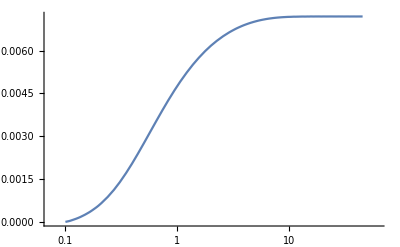

```mathematica
LogLinearPlot[deltaρa[x],{x,0.1,46}]
```

```mathematica
deltaρa[50]
```

0.00720043

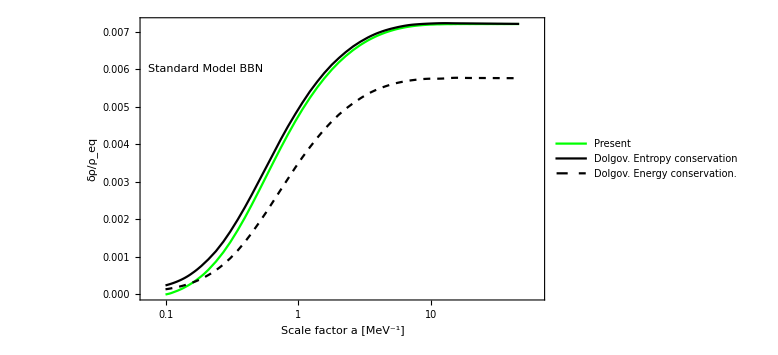

```mathematica
Show[LogLinearPlot[{deltaρa[x],deltaρaDolgovFunc[x],deltaρaDolgovFuncNonconserv[x]},{x,0.1,46},PlotRange->All(*{{0.1,100},{0,0.008}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δρ/ρ_eq"},PlotStyle->{{Thick,Green},{Black},{Dashed,Black}},Epilog->{Text["Standard Model BBN",{Log[0.2],0.006}]},ImageSize->Large,PlotLegends->{"Present","Dolgov. Entropy conservation","Dolgov. Energy conservation."}]]
```

```mathematica
Export["delta_rho.png",%]
```

delta_rho.png

#### Figure 1 from Hannestad&Madsen

```mathematica
TEllist=Transpose[linesEl][[2]];
```

```mathematica
ρeq0=(7 π^2)/240(#/1.40102)^4&/@TEllist;
```

```mathematica
deltaρT=Interpolation[Transpose[{TEllist,(ρlistρ-6ρeq)/ρlistρ}]]
```

Interpolation[Transpose[{Transpose[linesEl]⟦2⟧,{-1.04075×10^-6,0.0000103299,0.000023353,0.0000407992,0.0000587206,0.0000771159,0.0000955614,0.000116285,0.000137851,0.00016119,0.000186671,0.00021362,0.000240193,0.000269715,0.000300818,0.000331436,0.000365931,0.000401822,0.000437525,0.000477709,0.000517564,0.00056045,0.000606846,0.000653651,0.000702444,0.00075233,0.000805946,0.000862262,0.000918191,0.000978511,0.00104065,0.0011032,0.00117014,0.00123871,0.00130849,0.00137977,0.00145452,0.0015298,0.00160792,0.00168829,0.00176915,0.00185249,0.00193709,0.00202292,0.0021105,0.00219949,0.00228955,0.00238059,0.00247212,0.00256476,0.00265806,0.00275187,0.00284591,0.0029409,0.00303598,0.00313074,0.00322478,0.00332063,0.00341505,0.0035085,0.0036026,0.0036956,0.00378783,0.0038794,0.00397042,0.00406083,0.00414957,0.00423755,0.00432428,0.00441002,0.00449439,0.00457768,0.00465906,0.00473943,0.00482,0.00489648,0.00497289,0.00504886,0.00512131,0.00519063,0.00526158,0.00532874,0.00539856,0.00546198,0.0055267,0.00558788,0.00564869,0.00570737,0.00576737,0.00582242,0.00587795,0.00593043,0.00598241,0.00603125,0.0060809,0.0061289,0.00617362,0.00621806,0.00626188,0.00630305,0.00634301,0.00638301,0.00642039,0.00645716,0.00649265,0.00652744,0.00655956,0.00659112,0.00662137,0.00665068,0.00667936,0.00670713,0.0067332,0.00675811,0.00678202,0.00680497,0.00682748,0.00684863,0.00686871,0.00688751,0.00690562,0.00692366,0.00693992,0.00695556,0.00697034,0.00698438,0.00699829,0.00701097,0.00702243,0.0070337,0.00704353,0.00705348,0.00706288,0.00707142,0.00707911,0.00708594,0.00709302,0.00709916,0.00710473,0.00710996,0.0071144,0.00711861,0.00712256,0.00712605,0.00712886,0.00713189,0.00713465,0.00713583,0.00713726,0.00713977,0.00714187,0.0071411,0.00714252,0.00714372,0.00714487,0.00714619,0.00714691,0.00714573,0.00714633,0.00714812,0.00714719,0.00714963,0.00714893,0.00714813,0.00714923,0.00714912,0.00714959,0.00714927,0.00714828,0.00714931,0.00714946,0.0071487,0.00714903,0.0071492,0.00714936,0.00714955,0.00714909,0.00714884,0.0071487,0.0071494,0.00714956,0.00714884,0.00714926,0.00714837,0.00714884,0.0071493,0.00714929,0.00714837,0.00714895,0.00714893,0.00714913,0.00714844,0.007149,0.00714914,0.00714913,0.00714915,0.00714865,0.00714911,0.00714895,0.00714934,0.00714863,0.00714915,0.00714925,0.00714905,0.00714863,0.00714965,0.00714846,0.00714882,0.00714894,0.00714886,0.00714906,0.00714905,0.00714918,0.00714878,0.0071491,0.00714899,0.00714873,0.0071489,0.00714904,0.00714881,0.00714881,0.0071479,0.00714933,0.00715081,0.00714926,0.00715024,0.00714904,0.00714904,0.00714968,0.00714955,0.00714979,0.0071478,0.00714895,0.00714902,0.00714787,0.00714789,0.00714935,0.00714866,0.00714898,0.00714857,0.00714819,0.00714914,0.00714796,0.00714888,0.00714824,0.00714945,0.0071482,0.00714915,0.00714971,0.00714854,0.00714903,0.00714871,0.00714957,0.0071484,0.00714937,0.00714874,0.00714929,0.00714835,0.00714925,0.00714919,0.00714924,0.00714917,0.00714903,0.00714881,0.00714898,0.00714932,0.00714886,0.00714845,0.00714941,0.00714853,0.0071485,0.00714888,0.0071489,0.0071494,0.00714905,0.00714875,0.00714915,0.00714901,0.00714844,0.00714929,0.00714911,0.00714927,0.00714914,0.00714912,0.00714896,0.00714883,0.00714875,0.00714882,0.00714871,0.00714908,0.00714892,0.00714878,0.0071492,0.00714899,0.00715033,0.00714784,0.00714964,0.00715074,0.0071501,0.00714837,0.00715027,0.00714787,0.00714905,0.00714811,0.00714805,0.00714806,0.00714926,0.00714899,0.00714895,0.00714985,0.00714825,0.00714979}}]]

```mathematica
LogLogPlot[Abs[deltaρT[x]],{x,0.01,2}]
```

-Graphics-

```mathematica
deltaρTHannestad=Import["Hannestad_rho_case1.dat","HeaderLines"->1];
deltaρTHannestadFunc=Interpolation[deltaρTHannestad[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

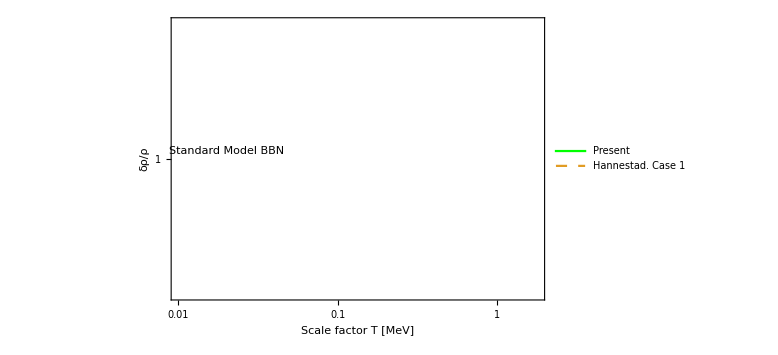

```mathematica
Show[LogLogPlot[{deltaρT[x],deltaρTHannestadFunc[x]},{x,0.01,1.8},PlotRange->{{0.01,1.8},{0,0.1}},Frame->True,FrameLabel->{"Scale factor T [MeV]","δρ/ρ"},PlotStyle->{{Thick,Green},{Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.02],0.003}]},ImageSize->Large,PlotLegends->{"Present","Hannestad. Case 1"}]]
```

```mathematica
Export["delta_rho_Hannestad.png",%];
```

## Teff

### Comraring with figure 3 of Hannestad et. al

```mathematica
aT=aEllist* TEllist;
```

```mathematica
pEl=
```

```mathematica
plotDataEl=Transpose[{yEl, distEl1}];
```